```mathematica
k=0.2;
m=0.6;
s=0.4;
K=1-k;
M=1-m;
S=1-s;

eq1=a+b+c+d+e+f==1;
eq2=a==k*1*1*a+k*1*S*b;
eq3=b==k*M*1*c+k*M*1*d+k*1*s*b;
eq4=c==k*m*1*c+k*m*S*d+K*1*S*b+K*1*1*a;
eq5=d==(k*m*s+K*M*1)*d+K*M*1*c+K*1*s*b+k*M*1*f+k*M*1*e;
eq6=e==1*m*1*e+K*m*S*d+K*m*1*c+1*m*S*f;
eq7=f==(1*m*s+K*M*1)*f+K*m*s*d+K*M*1*e;

analyticalResults = Solve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7},{a,b,c,d,e,f}]
```

{{a→0.00183711,b→0.0122474,c→0.0183711,d→0.122474,e→0.458311,f→0.38676}}

{{a→0.002,b→0.013,c→0.019,d→0.124,e→0.462,f→0.381}}

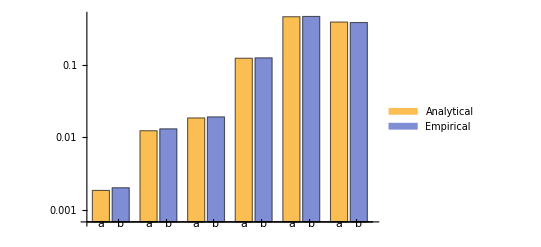

```mathematica
empResults = {{a-> 0.002, b->0.013, c-> 0.019, d -> 0.124, e-> 0.462, f-> 0.381}}
comparison=Transpose[{Values[First[analyticalResults]],Values[First[empResults]]}];

BarChart[comparison,ChartLabels->{"a","b","c","d","e","f"}, ChartLegends->{"Analytical","Empirical"}, ScalingFunctions->"Log"]
```